# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
colors=Append[Table[ColorData["Rainbow"][i],{i,{0.3,0.6,0.7,0.95}}],Gray]
```

{RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.6660832, 0.7430418, 0.32293540000000004],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

## Immune escape

```mathematica
escape=Import["../escape-score/escape_scores.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding
BA.2 | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.000089996 | 0
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.000089996 | 0
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.000089996 | 0
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.000089996 | 0
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.000089996 | 0
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.000089996 | 0
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.000089996 | 0
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.000089996 | 0
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.000089996 | 0
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.000089996 | 0
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.000089996 | 0
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.000089996 | 0
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.000089996 | 0
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.000089996 | 0
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.000089996 | 0
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.000089996 | 0
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.000089996 | 0
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.000089996 | 0
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.000089996 | 0
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.000089996 | 0
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.000089996 | 0
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.000089996 | 0
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.000089996 | 0
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.000089996 | 0
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.000089996 | 0
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.000089996 | 0
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.000089996 | 0
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.000089996 | 0
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.000089996 | 0
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.000089996 | 0
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.000089996 | 0
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.000089996 | 0
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.000089996 | 0
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.000089996 | 0
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.000089996 | 0
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.000089996 | 0
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.000089996 | 0
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.000089996 | 0
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.000089996 | 0
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.000089996 | 0
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.000089996 | 0
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.000089996 | 0
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.000089996 | 0
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.000089996 | 0
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.000089996 | 0
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.000089996 | 0
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.000089996 | 0
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.000089996 | 0
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.000089996 | 0
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.000089996 | 0
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.000089996 | 0
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.000089996 | 0
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.000089996 | 0
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.000089996 | 0
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.000089996 | 0
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.000089996 | 0
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.000089996 | 0
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.000089996 | 0
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.000089996 | 0
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.000089996 | 0
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.000089996 | 0
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.000089996 | 0
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.000089996 | 0
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.000089996 | 0
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.000089996 | 0
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.000089996 | 0
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.000089996 | 0
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.000089996 | 0
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.000089996 | 0
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.000089996 | 0
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.000089996 | 0
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.000089996 | 0
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.000089996 | 0
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.000089996 | 0
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.000089996 | 0
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.000089996 | 0
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.000089996 | 0
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.000089996 | 0
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.000089996 | 0
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.000089996 | 0
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.000089996 | 0
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.000089996 | 0
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.162048 | 0.13507
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.000089996 | 0
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.000089996 | 0
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.000089996 | 0
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973
BA.4.8 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.46306
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831
BA.5.2.15 | 22B (Omicron) | BA.5.2.15 | BA.5.2.15 | 0.386325 | 0.55831
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.22218
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339
BQ.1 | 22B (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197
BQ.1.1 | 22B (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831
XAB | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAA | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAD | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAF | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XAE | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.26796
XAH | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAC | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
XAJ | 21L (Omicron) | BA.2.12 | BA.2.12 | 0.386325 | 0.35483
XAL | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAG | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | -0.28094
XAP | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAR | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAK | 21L (Omicron) | BA.2 | BA.2 | 0.276938 | 1.15166
XAM | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0.75567
XAT | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
XAU | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XAN | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
XAW | 21L (Omicron) | BA.2 | BA.2 | 0.212 | 0.91409
XAV | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
XAS | 21L (Omicron) | B.1.1.529 | B.1.1.529 | 0.386325 | 0.55831
XAQ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XBB | recombinant | XBB | XBB | 0.907001 | 0.40687
XAZ | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
XG | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XE | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XH | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XK | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -3.62446
XN | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XJ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XL | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XR | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XM | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XQ | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XT | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.17271
XV | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.17271
XW | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XU | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | -0.09525
XZ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XY | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],_->colors[[5]] }
```

{21L (Omicron)→RGBColor[0.2979596, 0.5657928, 0.7522386000000001],22A (Omicron)→RGBColor[0.6660832, 0.7430418, 0.32293540000000004],22B (Omicron)→RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],22D (Omicron)→RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.60488 | 1.61477 | 1.59598
USA | BA.1 | 0.645363 | 0.650452 | 0.639626
USA | BA.1.1 | 0.676187 | 0.677868 | 0.674383
USA | BA.1.1.1 | 0.681272 | 0.704187 | 0.659729
USA | BA.1.1.10 | 0.764454 | 0.780794 | 0.747668
USA | BA.1.1.14 | 0.685506 | 0.699019 | 0.669258
USA | BA.1.1.16 | 0.732897 | 0.74639 | 0.71903
USA | BA.1.1.18 | 0.6427 | 0.649253 | 0.638077
USA | BA.1.1.2 | 0.618562 | 0.646551 | 0.593348
USA | BA.1.15 | 0.631348 | 0.63663 | 0.626012
USA | BA.1.15.2 | 0.678353 | 0.695708 | 0.662758
USA | BA.1.17.2 | 0.672173 | 0.689439 | 0.661663
USA | BA.1.18 | 0.669866 | 0.685806 | 0.656454
USA | BA.1.20 | 0.668941 | 0.678947 | 0.660721
USA | BA.2.1 | 1.0305 | 1.03585 | 1.02429
USA | BA.2.10 | 0.888939 | 0.89187 | 0.885896
USA | BA.2.10.1 | 0.887947 | 0.894037 | 0.88039
USA | BA.2.12 | 1.21695 | 1.22049 | 1.21295
USA | BA.2.12.1 | 1.22633 | 1.22703 | 1.22555
USA | BA.2.13 | 1.23431 | 1.23878 | 1.23087
USA | BA.2.13.1 | 1.3626 | 1.37049 | 1.35692
USA | BA.2.16 | 0.963368 | 0.978651 | 0.949116
USA | BA.2.18 | 1.21525 | 1.21804 | 1.21251
USA | BA.2.20 | 1.05199 | 1.05856 | 1.04674
USA | BA.2.21 | 0.998041 | 1.00338 | 0.992929
USA | BA.2.22 | 1.06598 | 1.07602 | 1.05744
USA | BA.2.23 | 1.10448 | 1.10872 | 1.10092
USA | BA.2.23.1 | 1.05147 | 1.05771 | 1.04372
USA | BA.2.26 | 0.926038 | 0.932043 | 0.921017
USA | BA.2.3 | 0.991522 | 0.99242 | 0.990333
USA | BA.2.3.10 | 1.00873 | 1.01842 | 0.99739
USA | BA.2.3.14 | 1.01222 | 1.0252 | 1.00106
USA | BA.2.3.17 | 0.977977 | 0.983129 | 0.97381
USA | BA.2.3.2 | 1.1192 | 1.13488 | 1.10612
USA | BA.2.3.4 | 0.987911 | 0.994387 | 0.980856
USA | BA.2.3.6 | 1.07895 | 1.0878 | 1.07096
USA | BA.2.31 | 1.04863 | 1.05376 | 1.04394
USA | BA.2.32 | 0.976821 | 0.983828 | 0.970379
USA | BA.2.36 | 1.18137 | 1.18532 | 1.17605
USA | BA.2.37 | 1.00375 | 1.00853 | 0.999355
USA | BA.2.38 | 1.36188 | 1.36599 | 1.35775
USA | BA.2.40.1 | 1.19859 | 1.20547 | 1.19051
USA | BA.2.41 | 1.19381 | 1.20323 | 1.18435
USA | BA.2.47 | 1.11306 | 1.12225 | 1.10068
USA | BA.2.48 | 1.17155 | 1.17521 | 1.16908
USA | BA.2.5 | 0.994307 | 1.00887 | 0.981211
USA | BA.2.52 | 1.26456 | 1.27431 | 1.2547
USA | BA.2.56 | 1.30233 | 1.30794 | 1.29736
USA | BA.2.59 | 1.11119 | 1.12083 | 1.10372
USA | BA.2.6 | 1.01387 | 1.02145 | 1.00808
USA | BA.2.65 | 1.0887 | 1.09134 | 1.08596
USA | BA.2.7 | 0.916003 | 0.918336 | 0.91303
USA | BA.2.72 | 1.13534 | 1.14155 | 1.12992
USA | BA.2.73 | 1.04044 | 1.04634 | 1.03068
USA | BA.2.75 | 2.15363 | 2.15736 | 2.15021
USA | BA.2.75.2 | 2.33824 | 2.34545 | 2.32854
USA | BA.2.76 | 1.59704 | 1.60217 | 1.59281
USA | BA.2.8 | 1.03873 | 1.04699 | 1.0292
USA | BA.2.9 | 1.0179 | 1.01864 | 1.01716
USA | BA.2.9.2 | 0.824011 | 0.82923 | 0.817358
USA | BA.2.9.3 | 1.23869 | 1.24641 | 1.2296
USA | BA.4 | 1.59483 | 1.59574 | 1.59366
USA | BA.4.1 | 1.57359 | 1.57437 | 1.57275
USA | BA.4.1.1 | 1.56453 | 1.56705 | 1.56202
USA | BA.4.1.6 | 1.54922 | 1.55169 | 1.5473
USA | BA.4.1.8 | 1.9791 | 1.98271 | 1.97484
USA | BA.4.2 | 1.59251 | 1.59428 | 1.59062
USA | BA.4.3 | 1.59705 | 1.60062 | 1.59334
USA | BA.4.4 | 1.58923 | 1.5902 | 1.5878
USA | BA.4.6 | 1.97078 | 1.97195 | 1.96986
USA | BA.5 | 1.80478 | 1.80574 | 1.80346
USA | BA.5.1 | 1.83377 | 1.83468 | 1.83274
USA | BA.5.1.1 | 1.74156 | 1.74272 | 1.74063
USA | BA.5.1.10 | 1.87741 | 1.87881 | 1.87567
USA | BA.5.1.12 | 2.00381 | 2.01142 | 1.99672
USA | BA.5.1.18 | 2.13788 | 2.14231 | 2.13433
USA | BA.5.1.19 | 1.77508 | 1.78287 | 1.76787
USA | BA.5.1.2 | 1.93341 | 1.93584 | 1.931
USA | BA.5.1.21 | 1.86622 | 1.87215 | 1.86022
USA | BA.5.1.3 | 1.836 | 1.8381 | 1.83361
USA | BA.5.1.5 | 2.07498 | 2.07821 | 2.07139
USA | BA.5.1.6 | 1.91492 | 1.91723 | 1.91274
USA | BA.5.1.7 | 2.03381 | 2.03971 | 2.0294
USA | BA.5.10.1 | 2.12163 | 2.12791 | 2.11608
USA | BA.5.2 | 1.90171 | 1.90282 | 1.90067
USA | BA.5.2.1 | 1.83554 | 1.83651 | 1.83467
USA | BA.5.2.16 | 1.95727 | 1.96352 | 1.95169
USA | BA.5.2.19 | 1.98479 | 1.99095 | 1.97916
USA | BA.5.2.2 | 1.80741 | 1.81113 | 1.8036
USA | BA.5.2.20 | 1.90338 | 1.90523 | 1.90121
USA | BA.5.2.21 | 1.8794 | 1.88046 | 1.87783
USA | BA.5.2.22 | 2.07402 | 2.07702 | 2.07096
USA | BA.5.2.3 | 1.93344 | 1.93677 | 1.93014
USA | BA.5.2.6 | 2.12846 | 2.13186 | 2.12442
USA | BA.5.2.8 | 1.9592 | 1.96552 | 1.95505
USA | BA.5.2.9 | 1.91719 | 1.91834 | 1.91597
USA | BA.5.3 | 1.61682 | 1.61923 | 1.61421
USA | BA.5.3.1 | 1.86086 | 1.86271 | 1.85878
USA | BA.5.5 | 1.65358 | 1.65448 | 1.65278
USA | BA.5.5.1 | 1.95564 | 1.9583 | 1.95327
USA | BA.5.5.2 | 1.79602 | 1.79931 | 1.79258
USA | BA.5.5.3 | 1.81496 | 1.81866 | 1.8111
USA | BA.5.6 | 1.76199 | 1.76294 | 1.76105
USA | BA.5.6.1 | 1.86285 | 1.86637 | 1.858
USA | BA.5.6.2 | 1.91831 | 1.92281 | 1.91464
USA | BA.5.8 | 1.74747 | 1.74979 | 1.74564
USA | BA.5.9 | 2.06359 | 2.06982 | 2.05808
USA | BE.1 | 1.77724 | 1.77852 | 1.77611
USA | BE.1.1 | 1.8544 | 1.85594 | 1.85312
USA | BE.1.1.1 | 2.16209 | 2.16884 | 2.15727
USA | BE.1.2 | 2.05672 | 2.06328 | 2.05212
USA | BE.2 | 1.80342 | 1.80568 | 1.80037
USA | BE.3 | 1.72963 | 1.73075 | 1.72832
USA | BF.1 | 1.68544 | 1.68775 | 1.68388
USA | BF.1.1 | 1.39841 | 1.40228 | 1.39364
USA | BF.10 | 1.84588 | 1.84733 | 1.84489
USA | BF.11 | 2.21592 | 2.21939 | 2.21158
USA | BF.13 | 1.9807 | 1.98382 | 1.97827
USA | BF.16 | 1.95196 | 1.95765 | 1.94673
USA | BF.21 | 1.777 | 1.77813 | 1.77567
USA | BF.25 | 2.04126 | 2.04943 | 2.03273
USA | BF.3 | 1.93053 | 1.93594 | 1.92632
USA | BF.4 | 1.80192 | 1.80457 | 1.80039
USA | BF.5 | 1.93634 | 1.93773 | 1.93478
USA | BF.7 | 2.27548 | 2.27832 | 2.27313
USA | BF.8 | 1.73725 | 1.73848 | 1.736
USA | BF.9 | 1.83384 | 1.83575 | 1.83188
USA | BG.2 | 1.27187 | 1.27268 | 1.27115
USA | BG.4 | 1.20803 | 1.21095 | 1.20456
USA | BG.5 | 1.31579 | 1.31811 | 1.31378
USA | BK.1 | 1.90137 | 1.90402 | 1.89875
USA | XAP | 1.11068 | 1.11749 | 1.10473
USA | XAS | 1.84615 | 1.85021 | 1.84138
USA | XE | 1.06645 | 1.07179 | 1.06071
USA | XZ | 1.12354 | 1.13122 | 1.11624
USA | other | 1.3495 | 1.35021 | 1.34879

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.2,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.19,BA.5.1.2,BA.5.1.21,BA.5.1.3,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.3,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.1,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.2,BE.3,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.16,BF.21,BF.3,BF.4,BF.5,BF.7,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,XAP,XAS,XE,XZ}

```mathematica
Length[pangoLineages]
```

120

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.939591

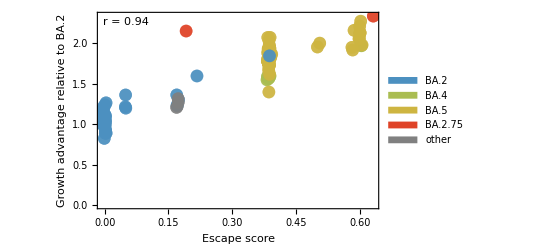

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.904475

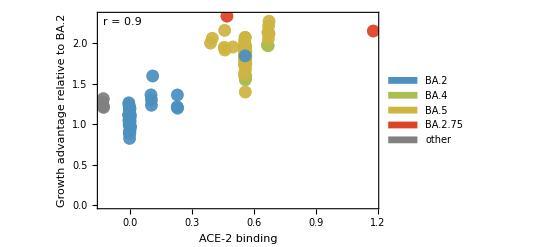

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.005]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.005]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.871994

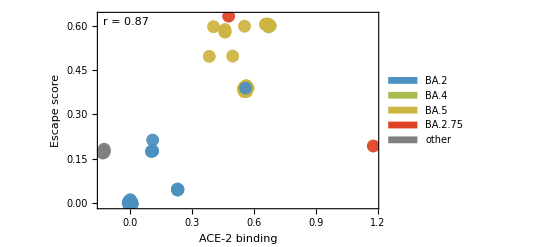

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_escape_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1 and binding X_2

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{x1,x2},{x1,x2}]
```

FittedModel[1.05806+1.22083 x1+0.514375 x2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.05806 | 0.0180027 | 58.7724 | 1.05513×10^-88
x1 | 1.22083 | 0.108504 | 11.2514 | 2.36907×10^-20
x2 | 0.514375 | 0.080601 | 6.38174 | 3.65127×10^-9